```mathematica
ClearAll["Global`*"]
```

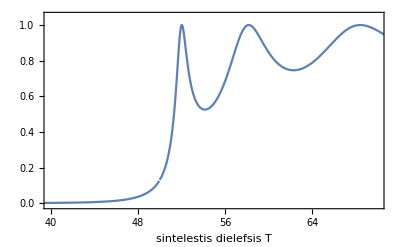

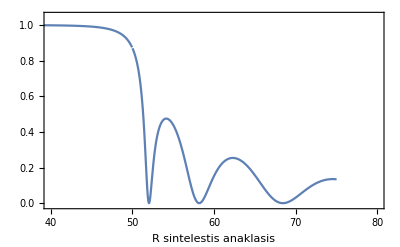

```mathematica
L1=10;L2=3;x1=0;x2=L1;V0=50;Catomic=26.247;Cnuclear=0.0482;c=Cnuclear;
(* πίνακας Μ ->συνθήκες ασυνέχειας του φράγματος*)(*k κυματάριθμος x θέση*)
M[k_,x_]={{Exp[I*k*x],Exp[-I*k*x]},{I*k*Exp[I*k*x],-I*k*Exp[-I*k*x]}};
(*πίνακας διάδοσης*)
P1[k_]=M[k,x1].Inverse[M[k,x2]];
(*πίνακας μεταφοράς*)
t[k0_,k1_]=Inverse[M[k0,0]].P1[k1].M[k0,x2];
(*υπολογισμος των συντελεστών*)
t11[k0_,k1_]=t[k0,k1][[1,1]];
(*όριο στο κ1->0 δηλαδή μέσα στο φράγμα*)
t11Limit[k0_]=Limit[t11[k0,k1],k1->0];
(* κυματάριθμοι συναρτήσει της ενέργειας*)
k0e[e_]=Sqrt[c*e];
k1e[e_]=Sqrt[c*(e-V0)];


t11teliko[e_]=Which[e≠V0,t11[k0e[e],k1e[e]],e==V0,t11Limit[k0e[e]]];
T[e_]=Sqrt[1/(t11teliko[e]*t11teliko[e]*)];
R[e_]:=1-T[e]
Plot[Evaluate[T[i]],{i,-5,80},PlotRange->{{40,70},{-0.01,1.05}},Frame->True,FrameLabel->T "sintelestis dielefsis"]
Plot[Evaluate[R[i]],{i,-5,75},PlotRange->{{40,80},{-0.01,1.05}},Frame->True,FrameLabel->R "sintelestis anaklasis"]
```